```mathematica
Mathematica code for :
  
  Alexander Heyde, David Rohde, Cameron S. McAlpine, Shuang Zhang, Friedrich F. Hoyer, Jeffrey M. Gerold, David Cheek, Yoshiko Iwamoto, Maximilian J. Schloss, Katrien Vandoorne, Oriol Iborra - Egea, Christian Muñoz - Guijosa, Antoni Bayes - Genis, Johannes G. Reiter, Morgan Craig, Filip K. Swirski, Matthias Nahrendorf, Martin A. Nowak, Kamila Naxerova. 
  
  Increased stem cell proliferation in atherosclerosis accelerates clonal hematopoiesis.
  
  Cell, 2021. In press.
```

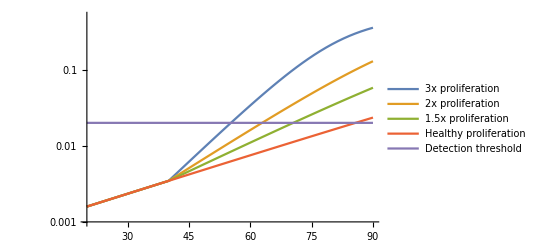

```mathematica
(*Table S2*)
(*All time measurements in years*)
b=365/28; (*Average baseline HSC proliferation rate*)
T=40; (*Age of onset for elevated HSC proliferation rate*)
F=.02; (*Detection frequency (minimum VAF)*)
ts=50; (*Mean age of baseline VAF data*)
fs=.0051; (*Frequency of the largest driver clone at age ts=50 years*)
s=.003; (*Selective effect of the largest driver clone*)
n=10^4; (*Number of HSCs*)

Clear[R]
t0=20;tf=90; (*Plot window*)
f0=.5/(1+(.5/fs-1)*Exp[b  s (ts-T)]);
LogPlot[{.5/(1+(.5/f0-1)*Exp[-b s (t-T)(1+(R-1) HeavisideTheta[t-T])])/.R->{3,2,1.5,1},.02}//Evaluate,{t,t0,tf},PlotRange->{.001,.5},PlotLegends->{"3x proliferation","2x proliferation","1.5x proliferation","Healthy proliferation","Detection threshold"}]
```

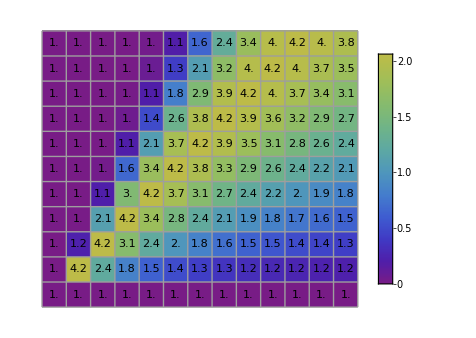

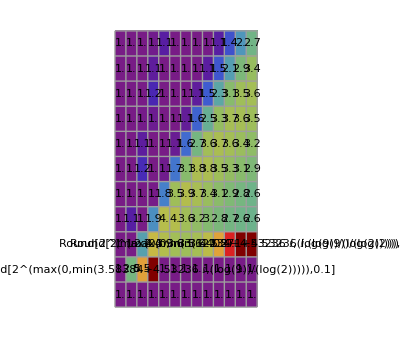

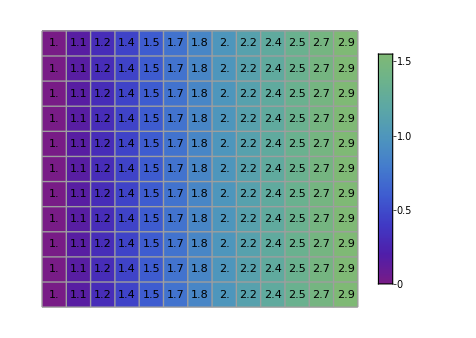

```mathematica
t1=70;(*Age at sequencing*)
R=2;(*HSC proliferation fold-increase*)
Clear[b,s]

Mx=13;My=11;(*Grid size*)
f0=2*.0005424; (*Initialization*)
f1=1/(1+(1/f0-1)Exp[-b s(ts-t0)]);
f2=1/(1+(1/f1-1)Exp[-b s(t1-ts)]);
f2R=1/(1+(1/f1-1)Exp[-R b s(t1-ts)]);
p2=1-CDF[BetaDistribution[f2(f2(1-f2)/Sqrt[f2/(s n)]-1),(1-f2)(f2(1-f2)/Sqrt[f2/(s n)]-1)],F];
p2R=1-CDF[BetaDistribution[f2R(f2R(1-f2R)/Sqrt[f2R/(s n)]-1),(1-f2R)(f2R(1-f2R)/Sqrt[f2R/(s n)]-1)],F];

(*Figure 3G*)
mat=Quiet[Reverse[Transpose[Table[Log2[f2R/f2]/.b->365/B,{B,1,600,599/(Mx-1)},{s,0,.12,.12/(My-1)}]]]];
Quiet[ArrayPlot[mat,PlotRange->All,ColorFunctionScaling->False,ColorFunction->ColorData[{"Rainbow",{0,Log2[9]}}],PlotLegends->BarLegend[Automatic,Ticks->logTicks[0,5]],FrameTicksStyle->Directive[Black,12],FrameLabel->{s,1/b},Epilog->{Black,MapIndexed[Text[#1,Reverse[#2-1/2]]&,Reverse[Round[2^mat,.1]],{2}]},Mesh->True]]

(*Figure 3H*)
mat=Quiet[Reverse[Transpose[Table[(Max[0,Min[Log2[9],Log2[p2R/p2]]]/.b->365/B)/.Indeterminate->0,{B,1,600,599/(Mx-1)},{s,0,.12,.12/(My-1)}]]]];
Quiet[ArrayPlot[mat,PlotRange->All,ColorFunctionScaling->False,ColorFunction->ColorData[{"Rainbow",{0,Log2[9]}}],FrameTicksStyle->Directive[Black,12],FrameLabel->{s,1/b},Epilog->{Black,MapIndexed[Text[#1,Reverse[#2-1/2]]&,Reverse[Round[2^mat,.1]],{2}]},Mesh->True]]

b=365/28; (*Average baseline HSC proliferation rate*)
s=.005; (*Selective effect of the largest driver clone*)
Clear[R,n]
f1=1/(1+(1/f1-1)Exp[-b s(ts-t0)]);
f2=1/(1+(1/f1-1)Exp[-b s(t1-ts)]);
f2R=1/(1+(1/f1-1)Exp[-R b s(t1-ts)]);

(*Supplemental*)
mat=Reverse[Transpose[Table[Log2[f2R/f2],{R,1,2.2,1.2/(Mx-1)},{n,30,70,40/(My-1)}]]];
ArrayPlot[mat,PlotRange->All,ColorFunctionScaling->False,ColorFunction->ColorData[{"Rainbow",{0,Log2[9]}}],PlotLegends->BarLegend[Automatic,Ticks->logTicks[0,5]],FrameTicksStyle->Directive[Black,12],FrameLabel->{ts,R},Epilog->{Black,MapIndexed[Text[#1,Reverse[#2-1/2]]&,Reverse[Round[2^mat,.1]],{2}]},Mesh->True]
```

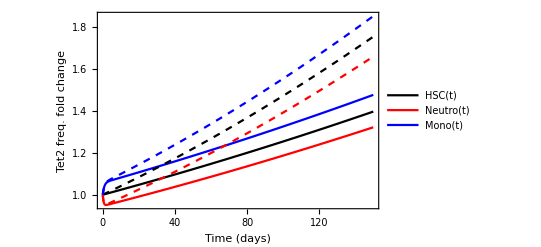

```mathematica
(*Table S3*)
(*All time measurements in days*)
y[t_]={HSC[t],Neutro[t],Mono[t]};(*Column headers*)
b0=1/17.5;(*Proliferation rate*)
L={Infinity,0.45,0.84};(*Mean lifespan*)
n={10^4,10^6,10^5.5};(*Population size*)
y0={.18,.19,.17};(*Initial Tet2 fraction*)

R=1.75;(*HSC proliferation fold-increase*)
s=.05; (*Selective effect of the largest driver clone*)
tf=150; (*Plot window end*)

one=y0^0;e1={1,0,0};n=n/(n.e1);d=1/L;
sol1=NDSolve[{y'[t]==(1+b0/(d.n))d*(one y1[t]-y[t])+b0 s e1 y1[t](1-y1[t])/(1+s y1[t]),y[0]==y0,y1[t]==y[t].e1},y[t],{t,0,tf}];
sol2=NDSolve[{y'[t]==(1+R b0/(d.n))d*(one y1[t]-y[t])+R b0 s e1 y1[t](1-y1[t])/(1+s y1[t]),y[0]==y0,y1[t]==y[t].e1},y[t],{t,0,tf}];

(*Figure 5C-E*)
Plot[{y[t]/y0/.sol1,y[t]/y0/.sol2}//Evaluate,{t,0,tf},PlotLegends->y[t],Frame->True,FrameLabel->{"Time (days)","Tet2 freq. fold change"},LabelStyle->Black,PlotStyle->{{Black},{Red},{Blue},{Black,Dashed},{Red,Dashed},{Blue,Dashed}}]
```